## Haplotypes and fitness

```mathematica
Clear["Global`*"]
```

```mathematica
makegenotype[hmat_,hpat_]:=Sort[Join[hmat,hpat]]
```

```mathematica
haplotypesF={{X,Af},{X,Am},{Xd,Af},{Xd,Am}};
```

```mathematica
haplotypesM={{X,Af},{X,Am},{Xd,Af},{Xd,Am},{Y}};
```

```mathematica
makegenotype[haplotypesF[[1]],haplotypesM[[5]]]
```

{Af,X,Y}

```mathematica
w[genotype_]:=Module[{sex,nxd,naf,w},
sex=If[Length[genotype]==4,f,m];
nxd=Count[genotype,Xd];
naf=Count[genotype,Af];
w=If[Count[{sex},f]==1,
{1-tf,1-h tf,1}[[1+naf]]*{1,1,1-cf}[[1+nxd]],
{1,1-tm}[[1+naf]]*{1,1-cm}[[1+nxd]]
];
Return[w]
]
```

```mathematica
segregation[hapNumMom_,hapNumDad_,hapNumGoal_]:=Module[{haploMom,haploDad,haploGoal,haploRec,haploNoRec,isFemale,hasDrive},
(* see what haplotypes we have *)
haploMom=haplotypesF[[hapNumMom]];
haploDad=haplotypesM[[hapNumDad]];
isFemale=haploDad!={Y};
hasDrive=Count[haploMom,Xd]==1;

(* what haplotype is desired *)
haploGoal=haplotypesM[[hapNumGoal]];

(* possible haplotypes in gametes when no recombination *)
haploNoRec={haploMom,haploDad};

(* we don't need to go through recombination if male *)
If[!isFemale,
Return[
If[hasDrive,If[Count[haploGoal,Y]==1,1-kdrive,kdrive],1/2]*Count[haploNoRec,haploGoal]
]
];

(* possible haplotypes in gametes with recombination *)
haploRec={{haploMom[[1]],haploDad[[2]]},{haploDad[[1]],haploMom[[2]]}};
Return[Simplify[Count[haploNoRec,haploGoal]/2 (1-r)+Count[haploRec,haploGoal]/2 r]]
]
```

## Recursions

Expression for W̄×y_(i,t+1):

```mathematica
WbarMytplus1=
Table[
Sum[
x[i]y[j]w[haplotypesF[[i]]]segregation[i,j,k],{i,1,Length[haplotypesF]},{j,5,5}
],{k,1,Length[haplotypesM]}
];
```

```mathematica
WbarMytplus1
```

{1/2 (1-tm) x[1] y[5],1/2 x[2] y[5],(1-cm) kdrive (1-tm) x[3] y[5],(1-cm) kdrive x[4] y[5],1/2 (1-tm) x[1] y[5]+1/2 x[2] y[5]+(1-cm) (1-kdrive) (1-tm) x[3] y[5]+(1-cm) (1-kdrive) x[4] y[5]}

```mathematica
WbarM=Total[WbarMytplus1];
```

```mathematica
ytplus1=WbarMytplus1/WbarM//Simplify;
```

```mathematica
WbarFxtplus1=Table[
Sum[
x[i]y[j]w[makegenotype[haplotypesF[[i]],haplotypesM[[j]]]]segregation[i,j,k],
{j,1,Length[haplotypesF]},{i,1,Length[haplotypesF]}
],
{k,1,Length[haplotypesF]}
];
```

```mathematica
WbarF=Total[WbarFxtplus1];
```

```mathematica
xtplus1=WbarFxtplus1/WbarF//Simplify;
```

```mathematica
WbarFxtplus1[[1]]
```

x[1] y[1]+1/2 (1-h tf) x[2] y[1]+1/2 x[3] y[1]+1/2 (1-r) (1-h tf) x[4] y[1]+1/2 (1-h tf) x[1] y[2]+1/2 r (1-h tf) x[3] y[2]+1/2 x[1] y[3]+1/2 r (1-h tf) x[2] y[3]+1/2 (1-r) (1-h tf) x[1] y[4]

```mathematica
primarySR=y[5]/(y[5]+Sum[x[i]y[j],{i,1,Length[haplotypesF]},{j,1,Length[haplotypesM]-1}]);
secondarySR=Sum[x[i]y[5]w[haplotypesF[[i]]],{i,1,Length[haplotypesF]}]/(Sum[x[i]y[5]w[haplotypesF[[i]]],{i,1,Length[haplotypesF]}]+Sum[x[i]y[j]w[makegenotype[haplotypesF[[i]],haplotypesM[[j]]]],{i,1,Length[haplotypesF]},{j,1,Length[haplotypesM]-1}]);
```

```mathematica
Dz=x[1]y[4]+x[4] y[1]-x[2] y[3]-x[3] y[2];
Demax[pe_,qe_]:=If[pe*(1-qe)<(1-pe)qe,pe*(1-qe),(1-pe)qe];
Dsmax[ps_,qs_]:=If[ps*(1-qs)<(1-ps)qs,ps*(1-qs),(1-ps)qs];
```

## Numerical analysis (auxiliary functions)

```mathematica
iterate[{tfs_,tms_,hs_},{cfs_,cms_},{kdrives_,rs_},maxt_]:=Module[{DataX,DataY,DataDz,DataP,sxtp1,ytp1,ysub,xsub,parsub,DataSR,srs},
(* allocate data *)
DataY=ConstantArray[ConstantArray[0,maxt+1],Length[haplotypesM]];
DataX=ConstantArray[ConstantArray[0,maxt+1],Length[haplotypesF]];
DataSR=ConstantArray[ConstantArray[0,maxt+1],2];
DataDz=ConstantArray[ConstantArray[0,maxt+1],4];
DataP=ConstantArray[ConstantArray[0,maxt+1],8];
parsub={tf->tfs,tm->tms,h->hs,cf->cfs,cm->cms,kdrive->kdrives,r->rs};
xtp1=xtplus1/.parsub;
ytp1=ytplus1/.parsub;
srs={primarySR,secondarySR}/.parsub;
DataY[[All,1]]={0.125,0.125,0.125,0.125,0.5};
DataX[[All,1]]={0.25,0.25,0.25,0.25};
For[iter=2,iter≤maxt+1,iter++,
ysub=Table[y[i]->DataY[[i,iter-1]],{i,1,Length[haplotypesM]}];
xsub=Table[x[i]->DataX[[i,iter-1]],{i,1,Length[haplotypesF]}];
DataX[[All,iter]]=xtp1/.ysub/.xsub;
DataY[[All,iter]]=ytp1/.ysub/.xsub;
DataSR[[All,iter]]=srs/.ysub/.xsub;
DataDz[[All,iter]]={Dz,Demax[x[1]+x[3],x[3]+x[4]],Dsmax[y[1]+y[3],y[3]+y[4]],Dz/(.5*(Demax[x[1]+x[3],x[3]+x[4]]+Dsmax[y[1]+y[3],y[3]+y[4]]))}/.ysub/.xsub;
DataP[[All,iter]]={x[1]+x[3],x[2]+x[4],x[1]+x[2],x[3]+x[4],y[1]+y[3],y[2]+y[4],y[1]+y[2],y[3]+y[4]}/.ysub/.xsub;
];
Return[Join[DataX,DataY,DataSR,DataDz,DataP]]
]
```

## Export to C

```mathematica
str="";
```

```mathematica
For[iter=1,iter≤Length[xtplus1],iter++,
str=str<>"xtp"<>ToString[iter]<>" = "<>ToString[CForm[xtplus1[[iter]]]]<>";\n\n";
];
For[iter=1,iter≤Length[ytplus1],iter++,
str=str<>"ytp"<>ToString[iter]<>" = "<>ToString[CForm[ytplus1[[iter]]]]<>";\n\n";
];
str=str<>"psr = "<>ToString[CForm[primarySR]]<>";\n\n";
str=str<>"ssr = "<>ToString[CForm[secondarySR]]<>";\n\n";
```

```mathematica
Export[$HomeDirectory<>"/Projects/drive/src/numerical/drive_expressions.txt",str]
```

/home/bram/Projects/drive/src/numerical/drive_expressions.txt

## Results

```mathematica
out=iterate[{0.4,0.5,0.5},{0.1,0.3},{0.9,0.01},5000];
```

```mathematica
out[[All,5]]
```

{0.237023,0.236616,0.250715,0.275646,0.100456,0.186348,0.130059,0.253694,0.329443,0.330699,0.293499,0.0110598,0.249568,0.140729,0.0566736}

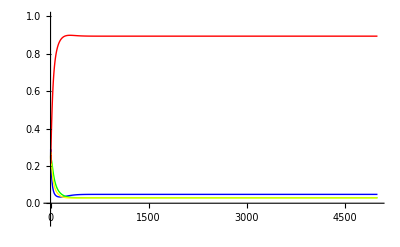

```mathematica
ListLinePlot[out[[1;;4]],PlotRange->{{0,Automatic},{-0.1,1.0}},PlotStyle->{Blue,Green,Yellow,Red,Black}]
```

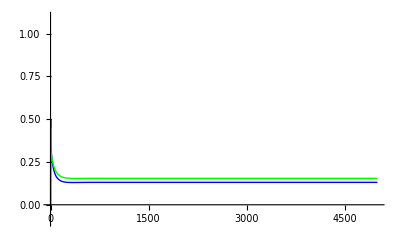

```mathematica
ListLinePlot[out[[10;;11]],PlotRange->{{0,Automatic},{-.1,1.1}},PlotStyle->{Blue,Green,Yellow,Red,Black}]
```

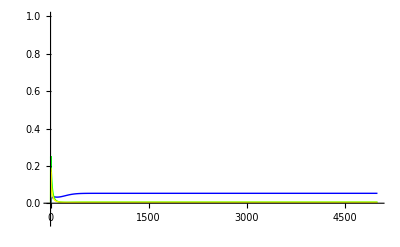

```mathematica
ListLinePlot[out[[12;;14]],PlotRange->{{0,Automatic},{-.1,1.0}},PlotStyle->{Blue,Green,Yellow,Red,Black}]
```

Calculate pe(1-qe)

```mathematica
out[[All,5000]][[18]](1-out[[All,5000]][[20]])
```

0.0746449

Calculate (1-pe)qe

```mathematica
out[[All,5000]][[19]]out[[All,5000]][[20]]
```

0.027864

Actual value Demax:

```mathematica
out[[12;;14,5000]]
```

{0.0530247,0.00583699,0.00511949}

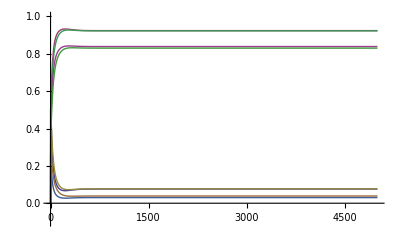

```mathematica
ListLinePlot[out[[16;;23]],PlotRange->{{0,Automatic},{-.1,1.0}}]
```

OK works.